```mathematica
Series[1/(1+x)^2,{x,0,5}]
```

1-2 x+3 x^2-4 x^3+5 x^4-6 x^5+O[x]^6

```mathematica
Series[1/(z[ω]-z[ω2])^2,{ω,ω2,2}]//Simplify
```

1/(z'[ω2]^2 (ω-ω2)^2)-z''[ω2]/(z'[ω2]^3 (ω-ω2))+(9 z''[ω2]^2-4 z'[ω2] z^(3)[ω2])/(12 z'[ω2]^4)-((6 z''[ω2]^3-6 z'[ω2] z''[ω2] z^(3)[ω2]+z'[ω2]^2 z^(4)[ω2]) (ω-ω2))/(12 z'[ω2]^5)+1/(240 z'[ω2]^6)(75 z''[ω2]^4-120 z'[ω2] z''[ω2]^2 z^(3)[ω2]+20 z'[ω2]^2 (z^(3)[ω2])^2+30 z'[ω2]^2 z''[ω2] z^(4)[ω2]-4 z'[ω2]^3 z^(5)[ω2]) (ω-ω2)^2+O[ω-ω2]^3

```mathematica
f[d_]:=(z'+d z'' + d^2/2 z''' )(z')/(d^2(z'+d/2 z''+d^2/6 z''')^2)
```

```mathematica
f[d_]:=(z''+d z''' + d^2/2 z'''' + d^3/6 z''''')(z')/(d^2(z'+d/2 z''+d^2/6 z'''+d^3/24 z'''')^2)-2(z'+d z''+d^2/2 z'''+d^3/6 z'''')^2z'/(d^3(z'+d/2 z''+d^2/6 z'''+d^3/24 z'''')^3)
```

```mathematica
Series[f[d],{d,0,0}]//Simplify
```

-2/d^3+(3 (z'')^3-4 z' z'' z^(3)+(z')^2 z^(4))/(12 (z')^3)+O[d]^1

```mathematica
D[w[z],{z,3}]/D[w[z],{z,1}]-3/2*(D[w[z],{z,2}]/D[w[z],{z,1}])^2//Simplify
```

0

```mathematica
(3(D[w[z],{z,2}])^3-4D[w[z],{z,1}]D[w[z],{z,2}]D[w[z],{z,3}]+(D[w[z],{z,1}])^2D[w[z],{z,4}])/(12(D[w[z],z])^3)//Simplify
```

0

## Bipartition

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[w1,w2,re]
gnrList[comb_]:=Flatten[Table[j[#-1],{comb[[#]]}]&/@Range[Length[comb]]]
mPerm[n_]:=Permutations[Range[n]]

gnrPair[combA_,combB_]:=Table[(gnrList[combA]/.{j->jA})[[ii]]*Permute[(gnrList[combB]/.{j->jB}),mPerm[Total@@{combA}] [[jj]]] [[ii]],{ii,1,Total@@{combA}},{jj,1,(Total@@{combA})!}]

f[m_,n_]:=D[1/(wA-wB)^2,{wA,m},{wB,n}]

OPEInside={jA[m_]jB[n_]->(f[m,n]/.{z1->wA,z2->wB})};
nOrderBi[combA_,combB_]:=If[Total@@{combA}≠Total@@{combB},0,
Total@@{Times@@(gnrPair[combA,combB]/.OPEInside)}]

OPE={mjA[comb1_]mjB[comb2_]->Evaluate[nOrderBi[comb1,comb2]],mjA[comb_]->0,mjB[comb_]->0};
one={w0->wA,j->jA,mj->mjA};
two = {w0->wB,j->jB,mj->mjB};

(*mj[{2,0}] means :j j:, mj[{3,0}] means :j j j:,mj[{1,1}] means :j ∂j:*)
```

```mathematica
w[z_]:=w0(1+z)/(1-z);
dw =w'[z]/.{z->0};
ddw = w''[z]/.{z->0};
dddw =w'''[z]/.{z->0};
ddddw =w''''[z]/.{z->0};

SchD=dddw/dw-3/2(ddw/dw)^2;
SchD2=(3(ddw)^3-4(dw)(ddw)(dddw)+(dw)^2 ddddw)/(12(dw)^3)//Simplify;
Print[" >> dw is: ", dw," ddw is: ",ddw," dddw is: ",dddw," ddddw is: ", ddddw]
Print[" >> Schwarzian derivative is: ", SchD, " SchD2 is: ", SchD2]

i=1;
J=(dw)mj[{1}];
pJ = 1/(√2)((dw)^2 mj[{0,1}]+(ddw)mj[{1}]);
p2J = 1/(2√3)((dw)^3 mj[{0,0,1}]+3(ddw)(dw)mj[{0,1}]+(dddw)mj[{1}]);
JJ=1/(√2)((dw)^2mj[{2}]+2 1/12 SchD);
pJJ=1/(√2)((dw)^3 mj[{1,1}]+(ddw)(dw)mj[{2}]+SchD2);
JJJ=1/(√6)((dw)^3mj[{3}]+3(dw)mj[{1}] 1/6 SchD);

States={i,J,pJ,JJ,p2J,pJJ,JJJ};
nameList = {"I","J","∂J","JJ","∂^2 J","∂JJ","JJJ"};

(* vertex operators *)
V[p_]:=(dw)^(p^2/2)v[p,0];
Vj[p_]:=(dw)^(p^2/2+1)v[p,1]+(dw)^(p^2/2) p/2 ddw/dw v[p,0];


one={w0->wA,j->jA,mj->mjA,v->vA};
two = {w0->wB,j->jB,mj->mjB,v->vB};
three = {w0->wC,j->jC,mj->mjC,v->vC};
```

>> dw is: 2 w0 ddw is: 4 w0 dddw is: 12 w0 ddddw is: 48 w0

>> Schwarzian derivative is: 0 SchD2 is: 0

```mathematica
Coeff = Table[Expand[(States[[i]]/.one) (States[[k]]/.two)]/.OPE/.{wA->2I,wB->-2I},{i,1,Length[States]},{k,1,Length[States]}];
Coeff//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1)

## Tripartition

```mathematica
Clear["Global`*"]
```

```mathematica
(* ---------------- three operators ------------------------- *)
mPerm[n_]:=Permutations[Range[n]]
gnrList[comb_]:=Flatten[Table[j[#-1],{comb[[#]]}]&/@Range[Length[comb]]]

(*Take n elements from all permutations of {B,C} to match with the n elements in {A}.
There are (#B+#C)! possibilities in the outcome.
*)
gnrMatch[combB_,combC_,n_,name_]:=
FoldPairList[TakeDrop,#,{n,Total@@{combB}+Total@@{combC}-n}]&/@(Join[gnrList[combB]/.{j->name[[2]]},gnrList[combC]/.{j->name[[3]]}][[#]]&/@mPerm[Total@@{combB}+Total@@{combC}])

(*Remaining pair. 
TODO: Only works for the case where unpair term has length 0,1,2*)
rmPair[op_]:=If[Mod[Length[op],2]==1,0,Times@@(op)/Length[op]!]

gnrTri[combA_,combB_,combC_,name_]:=Join[Table[(gnrList[combA]/.{j->name[[1]]})[[ii]]*#[[1,ii]],{ii,1,Total@@{combA}}],{rmPair[#[[2]]]}]&/@gnrMatch[combB,combC,Total@@{combA},name]

f[m_,n_]:=D[1/(z1-z2)^2,{z1,m},{z2,n}]
OPEInside={
jA[m_]jB[n_]->(f[m,n]/.{z1->wA,z2->wB}),jA[m_]jC[n_]->(f[m,n]/.{z1->wA,z2->wC}),jB[m_]jC[n_]->(f[m,n]/.{z1->wB,z2->wC}),jA[m_]^2->0,jB[m_]^2->0,jC[m_]^2->0,
jA[m_]jA[n_]->0,jB[m_]jB[n_]->0,jC[m_]jC[n_]->0};

reOrder[combA_,combB_,combC_]:=Module[{maxPosi,opNb,order,name,re},
opNb=Total[#]&/@{combA,combB,combC};
maxPosi=Position[opNb,Max[opNb]][[1,1]];
order={1,2,3};
name={jA,jB,jC};
If[maxPosi==1,
0,
{order[[{1,maxPosi}]]=order[[{maxPosi,1}]],
name[[{1,maxPosi}]]=name[[{maxPosi,1}]]}];
re = {{combA,combB,combC}[[order]],name}
];

(*TODO: looks ugly. Seems I cannot define another local variable. 
It gives error in the OPE replacement*)
nOrderTri[combA_,combB_,combC_]:=Module[{rt},
rt=If[
Mod[Total[combA]+Total[combB]+Total[combC],2]==1,0,
Total@@ {Times@@# &/@
(gnrTri[#[[1,1]],#[[1,2]],#[[1,3]],#[[2]]
]&[ reOrder[combA,combB,combC]]/.{OPEInside})[[1]]}
];
rt
]
nOrderTri::usage="
Comb: {n1,n2,n3} means there are n1 j, n2 ∂j, n3 ∂^2 J.
For example, {0,0,2} means :∂^2 J ∂^2 J:, {1,1} means :j ∂j: 
";


(*---------------------------two operators------------------------------------*)
gnrPair[combA_,combB_]:=Table[(gnrList[combA]/.{j->j1})[[ii]]*Permute[(gnrList[combB]/.{j->j2}),mPerm[Total@@{combA}] [[jj]]] [[ii]],{ii,1,Total@@{combA}},{jj,1,(Total@@{combA})!}]

nOrderBi[combA_,combB_,lb1_,lb2_]:=If[Total@@{combA}≠Total@@{combB},0,
Total@@{Times@@(gnrPair[combA,combB]/.{j1->lb1,j2->lb2}/.OPEInside)}
]
```

```mathematica
nOrderTri[{1},{3},{2}]
```

6/((wA-wB)^2 (wB-wC)^4)

```mathematica
w[z_]:=w0((1+z)/(1-z))^(2/3);
dw =w'[z]/.{z->0};
ddw = w''[z]/.{z->0};
dddw =w'''[z]/.{z->0};
ddddw =w''''[z]/.{z->0};

SchD=dddw/dw-3/2(ddw/dw)^2;
SchD2=(3(ddw)^3-4(dw)(ddw)(dddw)+(dw)^2 ddddw)/(12(dw)^3)//Simplify;
Print[" >> dw is: ", dw," ddw is: ",ddw," dddw is: ",dddw," ddddw is: ", ddddw]
Print[" >> Schwarzian derivative is: ", SchD, " SchD2 is: ", SchD2]

i=1;
J=(dw)mj[{1}];
pJ = 1/(√2)((dw)^2 mj[{0,1}]+(ddw)mj[{1}]);
p2J = 1/(2√3)((dw)^3 mj[{0,0,1}]+3(ddw)(dw)mj[{0,1}]+(dddw)mj[{1}]);
JJ=1/(√2)((dw)^2mj[{2}]+2 1/12 SchD);
pJJ=1/(√2)((dw)^3 mj[{1,1}]+(ddw)(dw)mj[{2}]+SchD2);
JJJ=1/(√6)((dw)^3mj[{3}]+3(dw)mj[{1}] 1/6 SchD);

States={i,J,pJ,JJ,p2J,pJJ,JJJ};
nameList = {"I","J","∂J","JJ","∂^2 J","∂JJ","JJJ"};

(* vertex operators *)
V[p_]:=(dw)^(p^2/2)v[p,0];
Vj[p_]:=(dw)^(p^2/2+1)v[p,1]+(dw)^(p^2/2) p/2 ddw/dw v[p,0];


one={w0->wA,j->jA,mj->mjA,v->vA};
two = {w0->wB,j->jB,mj->mjB,v->vB};
three = {w0->wC,j->jC,mj->mjC,v->vC};
```

>> dw is: (4 w0)/3 ddw is: (16 w0)/9 dddw is: (136 w0)/27 ddddw is: (1408 w0)/81

>> Schwarzian derivative is: 10/9 SchD2 is: 0

```mathematica
OPE={mjA[combA_]mjB[combB_]mjC[combC_]->nOrderTri[combA,combB,combC]};

OPEdbl={
mjA[comb1_]mjB[comb2_]->Evaluate[nOrderBi[comb1,comb2,jA,jB]],
mjB[comb1_]mjC[comb2_]->Evaluate[nOrderBi[comb1,comb2,jB,jC]],
mjA[comb1_]mjC[comb2_]->Evaluate[nOrderBi[comb1,comb2,jA,jC]]};

OPEsgl = {mjA[comb_]->0,mjB[comb_]->0,mjC[comb_]->0};

opeEpr[lv_]:=Expand[(States[[lv[[1]]]]/.one)*(States[[lv[[2]]]]/.two)*(States[[lv[[3]]]]/.three)]/.OPE/.OPEdbl/.OPEsgl;
opeRes[lv_]:=N[opeEpr[lv]/.{wA->Exp[I Pi/3],wB->Exp[-I Pi/3],wC->-1}//Simplify];
```

```mathematica
exmList = {{4,4,4},{4,2,2},{2,2,4},{2,4,2}};

Print[" >> Operators: ",nameList[[#[[1]]]],"  ",nameList[[#[[2]]]],"  ",nameList[[#[[3]]]],
". The result is: ", opeRes[#]]&/@exmList;
```

>> Operators: JJ  JJ  JJ. The result is: -0.448395

>> Operators: JJ  J  J. The result is: 0.419026

>> Operators: J  J  JJ. The result is: 0.419026

>> Operators: J  JJ  J. The result is: 0.419026

```mathematica
exmEle=5;
data = Table[opeRes[{exmEle,ii,jj}],{ii,1,7},{jj,1,7}]//Chop;
Grid[ArrayFlatten[{
{{{Style[nameList[[exmEle]],Bold]}},{nameList}},
{Transpose[{nameList}],data}
}],
Dividers->{#,#}&@Thread[Range[1,2,1]->True],
Frame->True
]
Print[" >> Is Hermitian? ", HermitianMatrixQ[data]]
```

∂^2 J | I | J | ∂J | JJ | ∂^2 J | ∂JJ | JJJ
I | 0 | -0.0380148 | 0.+0.31039 ⅈ | 0 | -0.522685 | 0 | -0.00862194
J | -0.0380148 | 0 | 0 | 0.0268805 | 0 | 0.-0.196197 ⅈ | 0
∂J | 0.-0.31039 ⅈ | 0 | 0 | 0.-0.0233027 ⅈ | 0 | 0.120146 | 0
JJ | 0 | 0.0268805 | 0.+0.0233027 ⅈ | 0 | -0.0663996 | 0 | -0.0170254
∂^2 J | -0.522685 | 0 | 0 | -0.0663996 | 0 | 0 | 0
∂JJ | 0 | 0.+0.196197 ⅈ | 0.120146 | 0 | 0 | 0 | 0.+0.026699 ⅈ
JJJ | -0.00862194 | 0 | 0 | -0.0170254 | 0 | 0.-0.026699 ⅈ | 0

>> Is Hermitian? True

```mathematica
lev={4,1,6};
N[opeEpr[lev]/.{wA->-1,wB->Exp[-I Pi/3],wC->Exp[I Pi/3]}//Simplify]//Chop
N[opeEpr[lev]/.{wA->-1,wB->Exp[I Pi/3],wC->Exp[-I Pi/3]}//Simplify]//Chop
N[opeEpr[lev]/.{wA->Exp[I Pi/3],wB->Exp[-I Pi/3],wC->-1}//Simplify]//Chop
N[opeEpr[lev]/.{wA->Exp[-I Pi/3],wB->Exp[I Pi/3],wC->-1}//Simplify]//Chop
N[opeEpr[lev]/.{wA->Exp[-I Pi/3],wB->-1,wC->Exp[I Pi/3]}//Simplify]//Chop
N[opeEpr[lev]/.{wA->Exp[I Pi/3],wB->-1,wC->Exp[-I Pi/3]}//Simplify]//Chop
```

0.-0.270328 ⅈ

0.+0.270328 ⅈ

0.+0.270328 ⅈ

0.-0.270328 ⅈ

0.+0.270328 ⅈ

0.-0.270328 ⅈ

#### Vertex operator

```mathematica
coeff[n__?NumericQ]:=Join[{1/(#!(n-#)!)},Table[I p1 XB,{#}], Table[I p2 XC,{n-#}]]&/@Range[0,n]

vGnrPair[combA_,vop_]:=Table[(gnrList[combA]/.{j->j1})[[ii]]*Permute[vop,mPerm[Total@@{combA}] [[jj]]] [[ii]],{ii,1,Total@@{combA}},{jj,1,(Total@@{combA})!}]

vf[m_,n_]:=D[-Log[z1-z2],{z1,m},{z2,n}]*If[m>0,I,1]*If[n>0,I,1]
vOPEInside={
jA[m_] XB->(vf[m+1,0]/.{z1->wA,z2->wB}),
jA[m_] XC->(vf[m+1,0]/.{z1->wA,z2->wC})};

vnOrderBi[combA_,vop_,lb1_]:=If[Total@@{combA}≠Length[vop],0,
Total@@{Times@@(vGnrPair[combA,vop]/.{j1->lb1}/.vOPEInside/.OPEInside)}
]

vopRes[combA_,cur_:{}]:=#[[1]]vnOrderBi[combA,Join[#[[2;;]],cur],jA]&/@coeff[Total[combA]-Length[cur]];
(*vopRes::usage="
Variables
--------
combA is the current operator, using the previous definition.
cur is optional input, which may have extra current in B and C.

Example input
------------
	vopRes[{2}]                 computes :jA jA: :e^(ipB XB) e^(ipC XC):. Gives {pC^2/(wA - wC)^2,(2 pB pC)/((wA - wB) (wA - wC)),pB^2/(wA - wB)^2}
	vopRes[{2},{jB[0]}]        computes :jA jA: :jB e^(ipB XB) e^(ipC XC):. Gives {(2 pC)/(wA - wB)^2,(2 pB)/(wA - wB)^3}
	vopRes[{3},{jB[0]}]        computes :jA jA jA: :jB e^(ipB XB) e^(ipC XC):
	vopRes[{2},{jB[0],jC[0]}]  computes :jA jA: :jB e^(ipB XB) jC e^(ipC XC):
";*)
vopCurRes[combA_,pB_,pC_,nB_,nC_]:=Hold[Total[vopRes[combA,Join[Table[jB[0],nB],Table[jC[0],nC]]]/.{p1->pB,p2->pC}]];
```

```mathematica
Clear[vOPE]
```

```mathematica
nOrderV[pA_,pB_,pC_]:=If[pA+pB+pC≠ 0,0,
(wA-wB)^(pA pB)(wB-wC)^(pB pC)(wA-wC)^(pA pC)
];

vOPE={vA[pA_,0]vB[pB_,0]vC[pC_,0]->nOrderV[pA,pB,pC],
mjA[combA_]vB[pB_,0]vC[pC_,0]->nOrderV[0,pB,pC]vopCurRes[combA,pB,pC,0,0],
mjA[combA_]vB[pB_,1]vC[pC_,0]->nOrderV[0,pB,pC](pC/(wB-wC)vopCurRes[combA,pB,pC,0,0]+vopCurRes[combA,pB,pC,1,0]),
mjA[combA_]vB[pB_,0]vC[pC_,1]->nOrderV[0,pB,pC](-pB/(wB-wC)vopCurRes[combA,pB,pC,0,0]+vopCurRes[combA,pB,pC,0,1]),
mjA[combA_]vB[pB_,1]vC[pC_,1]->nOrderV[0,pB,pC](- (pB pC)/(wB-wC)^2 vopCurRes[combA,pB,pC,0,0]+-pB/(wB-wC)vopCurRes[combA,pB,pC,1,0]+pC/(wB-wC)vopCurRes[combA,pB,pC,0,1]+vopCurRes[combA,pB,pC,1,1]),
vB[pB_,m_]vC[pC_,n_]->If[m==0 && n==0,nOrderV[0,pB,pC],0]};

vStates={V[2],Vj[2],V[-2],Vj[-2]};
vopeEpr[lv_]:=ReleaseHold[Expand[(States[[lv[[1]]]]/.one) (vStates[[lv[[2]]]]/.two)(vStates[[lv[[3]]]]/.three)]/.vOPE];

vopeRes[lv_]:=N[vopeEpr[lv]/.{wA->Exp[I Pi/3],wB->Exp[-I Pi/3],wC->-1}//Simplify];
```

```mathematica
(*nameList = {"I","J","∂J","∂^2 J","JJ","∂JJ","JJJ"};*)
(*vNameList = {"e^i2X", "je^i2X","e^-i2X", "je^-i2X"};*)
```

```mathematica
vNameList2 = {"e^i2X e^-i2X", "e^i2X je^-i2X","je^i2X e^-i2X","je^i2X je^-i2X"};
exmEle={{1,3},{1,4},{2,3},{2,4}};
data = Table[vopeRes[Join[{jj},exmEle[[ii]]]],{ii,1,4},{jj,1,7}]//Chop;
Grid[ArrayFlatten[{
{{{""}},{nameList}},
{Transpose[{vNameList2}],data}
}],
Dividers->{#,#}&@Thread[Range[1,2,1]->True],
Frame->True
]
```

| I | J | ∂J | JJ | ∂^2 J | ∂JJ | JJJ
e^i2X e^-i2X | 0.351166 | 0.-0.540655 ⅈ | 0 | -0.542607 | 0.-0.127171 ⅈ | 0 | 0.+0.400569 ⅈ
e^i2X je^-i2X | -0.468221 | 0.208098 | 0.+0.113274 ⅈ | -0.0613116 | 0.0845469 | 0.174397 | 0.248574
je^i2X e^-i2X | 0.468221 | 0.208098 | 0.-0.113274 ⅈ | 0.0613116 | 0.0845469 | -0.174397 | 0.248574
je^i2X je^-i2X | -0.624295 | 0 | 0 | -0.256146 | 0.+0.0548078 ⅈ | 0 | 0.+0.15502 ⅈ

```mathematica
lev={7,1,1};
N[vopeEpr[lev]/.{wA->-1,wB->Exp[-I Pi/3],wC->Exp[I Pi/3]}//Simplify]//Chop
N[vopeEpr[lev]/.{wA->-1,wB->Exp[I Pi/3],wC->Exp[-I Pi/3]}//Simplify]//Chop
N[vopeEpr[lev]/.{wA->Exp[I Pi/3],wB->Exp[-I Pi/3],wC->-1}//Simplify]//Chop
N[vopeEpr[lev]/.{wA->Exp[-I Pi/3],wB->Exp[I Pi/3],wC->-1}//Simplify]//Chop
N[vopeEpr[lev]/.{wA->Exp[-I Pi/3],wB->-1,wC->Exp[I Pi/3]}//Simplify]//Chop
N[vopeEpr[lev]/.{wA->Exp[I Pi/3],wB->-1,wC->Exp[-I Pi/3]}//Simplify]//Chop
```

```mathematica
opeRes[{1,2,3}]
```

0.+0.322567 ⅈ

```mathematica
(*nameList = {"I","J","∂J","JJ","∂^2 J","∂JJ","JJJ"};*)
(*vNameList = {"e^i2X", "je^i2X","e^-i2X", "je^-i2X"};*)
eS={0,1,2,2,3,3,3,2,3,2,3};

opeEprAll[l1_,l2_,l3_,ep_:0]:=Exp[-ep(eS[[l1]]+eS[[l2]]+eS[[l3]])] 
*Piecewise[{
{opeRes[{l1,l2,l3}],l1≤7 && l2≤7&&l3≤7},
{vopeRes[{l1,l2-7,l3-7}],l1≤7&&l2>7&&l3>7},
{vopeRes[{l2,l3-7,l1-7}],l1>7&&l2≤7&&l3>7},
{vopeRes[{l3,l1-7,l2-7}],l1>7&&l2>7&&l3≤7}
},0]
```

```mathematica
ep=0.02;
```

```mathematica
stRange=Range[1,7];
nSt=Length[stRange];
opeTable=Table[opeEprAll[ii,jj,kk,ep],{ii,stRange},{jj,stRange},{kk,stRange}];
```

```mathematica
M[α_,αp_]:=Sum[opeTable[[α,ii,jj]]*Conjugate[opeTable[[αp,ii,jj]]],{ii,1,nSt},{jj,1,nSt}]
reM=Table[M[ii,jj],{ii,1,nSt},{jj,1,nSt}]//Chop;
reM=reM/Tr[reM];
```

```mathematica
CUTOFF=10^-8;
vNEnt[M_]:=Total[If[CUTOFF≤#≤1-CUTOFF,-#*Log[#],0]&/@(#/Total[#]&@Eigenvalues[M])]

RefEnt[M_,nSt_]:=Module[{eigM,dM,vec,sqrtRho,reShapeSqrtRho,tildeMfun,tildeM,re},
eigM=Eigensystem[M];
dM=eigM[[1]]//Chop;
vec=eigM[[2]];
vec=Normalize[#]&/@vec;
(*Conjugate[V].reM2.Transpose[V]//Chop//MatrixForm*)

sqrtRho=Transpose[vec].DiagonalMatrix[Sqrt[dM]].Conjugate[vec]//Chop;
reShapeSqrtRho=ArrayReshape[sqrtRho,{nSt,nSt,nSt,nSt}];
tildeMfun[α_,αp_,tα_,tαp_]:=Sum[reShapeSqrtRho[[α,β,αp,βp]]*Conjugate[reShapeSqrtRho[[tα,β,tαp,βp]]],{β,1,nSt},{βp,1,nSt}];

tildeM=Table[tildeMfun[α,αp,tα,tαp],{α,1,nSt},{αp,1,nSt},{tα,1,nSt},{tαp,1,nSt}]//Chop;
tildeM =ArrayReshape[tildeM,{nSt^2,nSt^2}];
re = vNEnt[tildeM];
re
]
```

```mathematica
markovGap[ep_,stRange_]:=Module[{nSt,opeTable,M2,reM2,h},

nSt=Length[stRange];
opeTable=Table[opeEprAll[ii,jj,kk,ep],{ii,stRange},{jj,stRange},{kk,stRange}];
M2[α_,β_,αp_,βp_]:=Sum[opeTable[[α,β,jj]]*Conjugate[opeTable[[αp,βp,jj]]],{jj,1,nSt}];
reM2=Table[M2[α,β,αp,βp],{α,1,nSt},{β,1,nSt},{αp,1,nSt},{βp,1,nSt}]//Chop;
reM2 =ArrayReshape[reM2,{nSt^2,nSt^2}];
(*Print[" >> reM2 is hermitian? ", HermitianMatrixQ[reM2]];*)

h =RefEnt[reM2,nSt] -vNEnt[reM2];
h
]
```

```mathematica
markovGap[0.02,Range[1,11]]
```

>> reM2 is hermitian? True

1.11091

```mathematica
epAll=Range[0,1,0.02];
hAll= markovGap[#,Join[Range[1,11]]]&/@epAll;
```

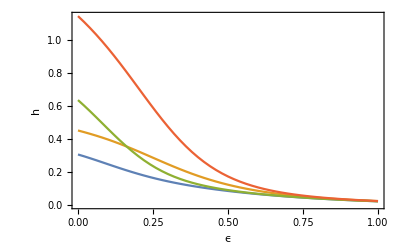

```mathematica
ListLinePlot[{Transpose[{epAll,hAll3}],Transpose[{epAll,hAll2}],Transpose[{epAll,hAll1}],Transpose[{epAll,hAll}]},
Frame->True,FrameLabel->{"ϵ","h"}]
```

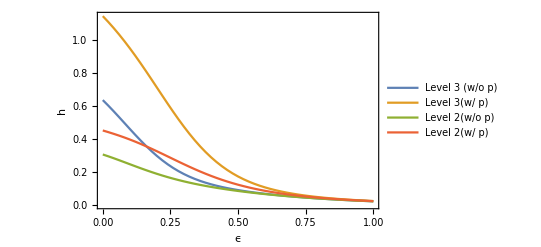

```mathematica
ListLinePlot[{Transpose[{epAll,hAll}],Transpose[{epAll,hAll2}],Transpose[{epAll,hAll3}],Transpose[{epAll,hAll4}]},
Frame->True,FrameLabel->{"ϵ","h"},PlotLegends->{"Level 3 (w/o p)","Level 3(w/ p)","Level 2(w/o p)","Level 2(w/ p)"}]
```

```mathematica
N[Log[2]/3]
```

0.231049

#### Miscellaneous

```mathematica
test=Subsets[Range[4],{2}]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

```mathematica
DeleteCases[Range[4],Alternatives@@#]&/@test
```

{{3,4},{2,4},{2,3},{1,4},{1,3},{1,2}}

```mathematica
w1= Exp[I Pi/3];
w2 = Exp[-I Pi/3];
w3 = Exp[-I Pi];
test=(16/9)^3 1/((w1-w2)^2(w1-w3)^2(w2-w3)^2)+(16/9)^2 5/54((w1 w2)^2 1/(2(w1-w2)^4)+(w1 w3)^2 1/(2(w1-w3)^4)+(w3 w2)^2 1/(2(w3-w2)^4))+(5/54)^3//Simplify
```

-8321/52488

```mathematica
N[test]*8/(2√2)//Simplify
```

-0.448395